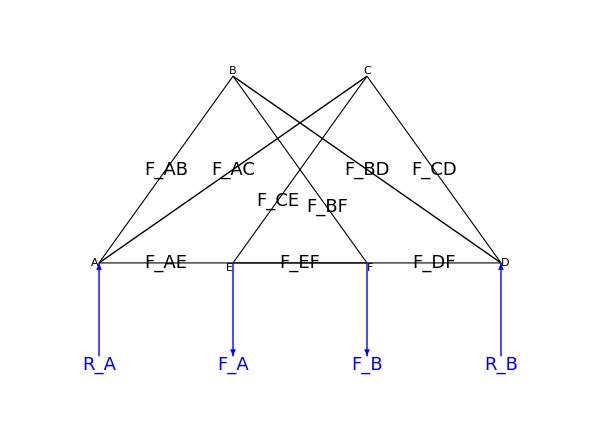

```mathematica
Module[{w,h,colC,colT},
w=5;h=5;
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{2*w,0},{w,h}}],Polygon[{{3*w,0},{w,0},{2*w,h}}]},
Line[{{w,h},{3*w,0}}],Line[{{2*w,h},{0,0}}],

{Blue,
Arrow[{{w,0},{w,-h/2}}],Arrow[{{2*w,0},{2*w,-h/2}}],
Text[Style[Subscript[Style["F",Italic],#1],18],{#2,-h/2},{0,1.2}]&@@@{{"A",w},{"B",2*w}},
Arrow[{{0,-h/2},{0,0}}],Arrow[{{3*w,-h/2},{3*w,0}}],
Text[Style[Subscript[Style["R",Italic],#1],18],{#2,-h/2},{0,1.2}]&@@@{{"A",0},{"B",3*w}}},

(*Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{1,{w/2,h/2}},{2,{w+0.6*w,0.4*h}},{3,{w/2,0}},{4,{w+w/3,h/3}},{5,{2*w+w/2,h/2}},{6,{2*w+w/2,0}},{7,{w+w/2,0}},{8,{(w+3*w)/2,h/2}},{9,{w,h/2}}},*)
Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15],#2,#3]&@@@{
{"A",{0,0},{1,0}},{"B",{w,h},{0,-1}},{"C",{2*w,h},{0,-1}},{"D",{3*w,0},{-1,0}},{"E",{w,0},{1,1.2}},{"F",{2*w,0},{-1,1.2}}},

(*{colT,Arrowheads@{-0.035,0.035},
Arrow[{{0,0},{w,0}}],Arrow[{{w,h},{2*w,0}}],Arrow[{{2*w,h},{w,0}}],Arrow[{{3*w,0},{2*w,0}}],Arrow[{{w,0},{2*w,0}}]},

{colC,Arrowheads@{{0.035,0.315},{-0.035,0.675}},
Arrow[{{0,0},{w,h}}],Arrow[{{0,0},{2*w,h}}],Arrow[{{w,h},{3*w,0}}],Arrow[{{2*w,h},{3*w,0}}]},*)

Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{"AB",{w/2,h/2}},{"BF",{w+0.7*w,0.3*h}},{"AE",{w/2,0}},{"CE",{w+w/3,h/3}},{"CD",{2*w+w/2,h/2}},{"DF",{2*w+w/2,0}},{"EF",{w+w/2,0}},{"BD",{(w+3*w)/2,h/2}},{"AC",{w,h/2}}},
},PlotRange->{{-1.65,16.65},{-3.3,6}},ImageSize->{600,425}]
]
```